# Scalar Self Force Tutorial

This tutorial shows how to compute the scalar self force (SSF) for a scalar charge  q in a circular orbit around a Schwarzschild black hole. The SSF is defined as  F_α=q ∇_α ϕ= ∑_l F_α^l. This tutorial follows https://arxiv.org/pdf/1003.1860.

Load the Teukolsky package:

```mathematica
<<Teukolsky`
```

## Field, time component F_t and radial component F_r

First let's set the system parameters. For simplicity, we'll work with a Schwarzschild black hole (a=0) and a circular orbit (e = 0) in this tutorial.

```mathematica
a0=0;
p0=14.0`50; (* The input precision is set here to 50. higher l-modes might need higher precision.*)
e0=0;
x0=1;
```

```mathematica
orbit=KerrGeoOrbit[a0,p0,e0,x0];
```

```mathematica
lmax= 25;
```

```mathematica
numOfModes=Sum[1,{l,1,lmax},{m,-l,l}]
```

675

Now let’s compute all the modes up to l_max for this orbit. We will do this in parallel to speed things up. (N.B: It could be further speed up by computing only the m≥ 0 modes only and use the mode symmetries to compute the m < 0 contributions) .

```mathematica
LaunchKernels[];
ParallelNeeds["Teukolsky`"]
i=0;SetSharedVariable[i]
```

```mathematica
Monitor[modeList = Flatten@ParallelTable[i++; TeukolskyPointParticleMode[0, l, m, orbit], {l, 0, lmax}, {m, -l, l}], ToString[i] <> "/" <> ToString[numOfModes]];
```

Example of output:

```mathematica
modeList[[1]]
modeList[[2]]
```

TeukolskyMode[…]

TeukolskyMode[…]

From the TeukolskyMode functions we can extract the useful quantities, e.g.,

```mathematica
modeList[[2]]["l"]
modeList[[2]]["ω"]
```

1

-0.01909008870803031319175382006283953725385724391724

Let's define a convenience function to select all lm-modes with a given l

```mathematica
modes[l_]:=Select[modeList,#["l"]==l&]
```

```mathematica
modes[0]
modes[1]
```

{TeukolskyMode[…]}

{TeukolskyMode[…],TeukolskyMode[…],TeukolskyMode[…]}

We now define functions to compute the modes of the field Φ, time component of the force F_t and the radial component of the force F_r at the particle.

```mathematica
Φ[mode_TeukolskyMode]:=mode["ExtendedHomogeneous"->"ℐ"][p0]SphericalHarmonicY[mode["l"],mode["m"],π/2,0]
```

```mathematica
Ft[mode_TeukolskyMode]:= -I mode["ω"]mode["ExtendedHomogeneous"->"ℐ"][p0]SphericalHarmonicY[mode["l"],mode["m"],π/2,0]
```

We select  "ℐ" in the ExtendedHomogeneous functions with sign=+1:

```mathematica
Fr[mode_TeukolskyMode,sign_]:=mode["ExtendedHomogeneous"->If[sign==+1,"ℐ","ℋ"]]'[p0]SphericalHarmonicY[mode["l"],mode["m"],π/2,0]
```

```mathematica
Φl=Table[{l,Re[Total[Φ/@modes[l]]]},{l,1,lmax}];
```

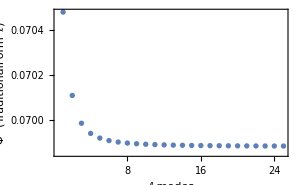

```mathematica
ListPlot[Φl,Frame->True,PlotRange->All,FrameStyle->Black, FrameLabel->{Style["ℓ-modes",20,FontFamily->"Latin Modern Roman"],Style["Φ^(TraditionalForm`ℓ)",20,FontFamily->"Latin Modern Roman"]},ImageSize->300]
```

Above we see that, for high-l, the retarded modes of the field tend to a constant, as expected. This can be regularized to compute a regular field, but we won't do that in this tutorial.

```mathematica
Ftl=Table[{l,Total[Ft/@modes[l]]},{l,1,lmax}];
```

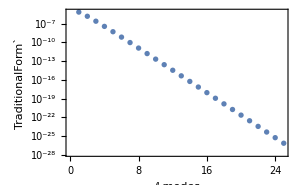

```mathematica
ListLogPlot[Ftl,Frame->True,FrameStyle->Black, FrameLabel->{Style["ℓ-modes",20,FontFamily->"Latin Modern Roman"],Style["TraditionalForm`",20,FontFamily->"Latin Modern Roman"]},ImageSize->300]
```

By plotting on a log plot above, we see that magnitudes of the l-modes of F_t fall of exponentially, as expected.

Let's compute the sum and compare it with the value in https://arxiv.org/pdf/1003.1860: 9.23672660e−6:

```mathematica
FtTotal=Re[Total[Ftl[[All,2]]]]
```

9.2367266072862558388547105×10^-6

Nice! Now, for the radial component:

```mathematica
Frl=Table[{l,Total[Fr[#,+1]&/@modes[l]]},{l,0,lmax}];
```

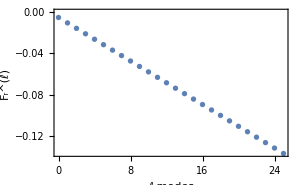

```mathematica
ListPlot[Frl,Frame->True,FrameStyle->Black, FrameLabel->{Style["ℓ-modes",20,FontFamily->"Latin Modern Roman"],Style["F_r^(ℓ)",20,FontFamily->"Latin Modern Roman"]},ImageSize->300]
```

Above we see that the modes of F_r are growing linearly as expected. This means the sum over the l-modes of the unregularized radial force diverges. To get a physically meaningful result we need to regularize F_r.

## Regularized F_r

Here we regularize Fr, so that:   F_r^self =  ∑_(l=0)^∞ F_r^((reg)l)  , where F_r^((reg)l) = F_r^l  - F_r[-1]^l-F_r[0]^l-F_r[2]^l-F_r[4]^l-F_r[6]^l  and the analytic "regularization parameters" (F_r[-1]^l,F_r[0]^l,F_r[2]^l,F_r[4]^l,F_r[6]^l) are computed in https://arxiv.org/pdf/1204.0794, and available electronically here: https://github.com/BlackHolePerturbationToolkit/RegularizationParameters

F_r[]^l: regularization  parameters

```mathematica
M=1;
r0=p0;
E0=(1-2 M/r0)√(r0/(r0-3M));
L=r0 √(M/(r0-3M)); 
ur=0;
```

#### F_a[-1]

```mathematica
Flr[-1]=-(E0 r0 (1+2 l) Sign[+1])/(2 (-2 M+r0) (L^2+r0^2));
```

#### F_a[0]

```mathematica
Flr[0]=((2 E0^2 r0^3+(2 M-r0) (L^2+r0^2)) EllipticE[L^2/(L^2+r0^2)]+(-E0^2 r0^3+(2 M-r0) (L^2+r0^2)) EllipticK[L^2/(L^2+r0^2)])/(π r0 (-2 M+r0) (L^2+r0^2)^(3/2));
```

#### F_a[2]

```mathematica
Flr[2]=((-8 E0^4 (L-r0) r0^10 (L+r0)+4 E0^2 r0^3 (L^2+r0^2) (9 L^6 M+26 L^4 M r0^2+23 L^2 M r0^4+L^2 r0^5+14 M r0^6-3 r0^7)+(2 M-r0) (L^2+r0^2)^2 (28 L^6 M+82 L^4 M r0^2+82 L^2 M r0^4-L^2 r0^5+32 M r0^6-3 r0^7)) EllipticE[L^2/(L^2+r0^2)]+(E0^4 r0^10 (3 L^2-5 r0^2)-E0^2 r0^5 (L^2+r0^2) (18 L^4 M+34 L^2 M r0^2+L^2 r0^3+32 M r0^4-7 r0^5)-(2 M-r0) r0^2 (L^2+r0^2)^2 (14 L^4 M+28 L^2 M r0^2+16 M r0^4-r0^5)) EllipticK[L^2/(L^2+r0^2)])/(2 (-1+2 l) (3+2 l) π r0^6 (-2 M+r0) (L^2+r0^2)^(7/2));
```

#### F_a[4]

```mathematica
Flr[4]=(3 ((30 E0^6 r0^19 (23 L^4-82 L^2 r0^2+23 r0^4)-E0^4 r0^8 (L^2+r0^2) (89600 L^12 M+438272 L^10 M r0^2+856504 L^8 M r0^4+837552 L^6 M r0^6+411938 L^4 M r0^8+495 L^4 r0^9+92836 L^2 M r0^10-3690 L^2 r0^11-902 M r0^12+1575 r0^13)+8 E0^2 r0^3 (L^2+r0^2)^2 (5120 L^14 M^2-35200 L^12 M^2 r0^2+26720 L^12 M r0^3-227368 L^10 M^2 r0^4+123200 L^10 M r0^5-456300 L^8 M^2 r0^6+225979 L^8 M r0^7-434510 L^6 M^2 r0^8+206277 L^6 M r0^9-203983 L^4 M^2 r0^10+94211 L^4 M r0^11-40376 L^2 M^2 r0^12+18367 L^2 M r0^13-135 L^2 r0^14-571 M^2 r0^14-146 M r0^15+135 r0^16)+(2 M-r0) (L^2+r0^2)^3 (40960 L^14 M^2-86016 L^12 M^2 r0^2+116480 L^12 M r0^3-860224 L^10 M^2 r0^4+510080 L^10 M r0^5-1780112 L^8 M^2 r0^6+882400 L^8 M r0^7-1657392 L^6 M^2 r0^8+752340 L^6 M r0^9-743164 L^4 M^2 r0^10+316100 L^4 M r0^11+30 L^4 r0^12-136236 L^2 M^2 r0^12+53200 L^2 M r0^13+75 L^2 r0^14-3120 M^2 r0^14+160 M r0^15+165 r0^16)) EllipticE[L^2/(L^2+r0^2)]+(-15 E0^6 r0^19 (15 L^4-82 L^2 r0^2+31 r0^4)+E0^4 r0^10 (L^2+r0^2) (44800 L^10 M+179936 L^8 M r0^2+272908 L^6 M r0^4+187126 L^4 M r0^6+135 L^4 r0^7+55232 L^2 M r0^8-1710 L^2 r0^9+118 M r0^10+1035 r0^11)-(2 M-r0) r0^2 (L^2+r0^2)^3 (20480 L^12 M^2-60928 L^10 M^2 r0^2+58240 L^10 M r0^3-375840 L^8 M^2 r0^4+204080 L^8 M r0^5-564472 L^6 M^2 r0^6+265360 L^6 M r0^7-350956 L^4 M^2 r0^8+152380 L^4 M r0^9-84276 L^2 M^2 r0^10+33740 L^2 M r0^11+15 L^2 r0^12-3120 M^2 r0^12+640 M r0^13+75 r0^14)-E0^2 r0^5 (L^2+r0^2)^2 (20480 L^12 M^2-158720 L^10 M^2 r0^2+106880 L^10 M r0^3-769632 L^8 M^2 r0^4+399280 L^8 M r0^5-1159632 L^6 M^2 r0^6+559556 L^6 M r0^7-755876 L^4 M^2 r0^8+352004 L^4 M r0^9-196524 L^2 M^2 r0^10+89680 L^2 M r0^11-405 L^2 r0^12-5528 M^2 r0^12+512 M r0^13+675 r0^14)) EllipticK[L^2/(L^2+r0^2)]))/(40 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π r0^13 (-2 M+r0) (L^2+r0^2)^(11/2));
```

#### F_a[6]

```mathematica
Flr[6]=(-1800 √2)/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))(((11550720000 L^28 M^4-10936320000 L^28 M^3 r0+737280 L^26 M^2 (3500 L^2+127167 M^2) r0^2+122880 (-639361+79800 E0^2) L^26 M^3 r0^3-4096 L^24 M^2 (150 (-18471+7480 E0^2) L^2-73805219 M^2) r0^4+2048 L^24 M (1097250 L^2+(-89756449+32656620 E0^2) M^2) r0^5+640 L^22 M^2 (16 (-2809627-2053380 E0^2+196800 E0^4) L^2+625211897 M^2) r0^6-64 L^22 M (84000 (-4195+894 E0^2) L^2-(1348765243+2439064160 E0^2) M^2) r0^7+64 L^20 M^2 ((-5439619239+343826592 E0^2+158518400 E0^4) L^2-3908647817 M^2) r0^8+32 L^20 M (875 (3659665-1583232 E0^2+104448 E0^4) L^2+(46847905117+296613362 E0^2) M^2) r0^9+32 L^18 M^2 ((-38854641925+12153454906 E0^2+184100608 E0^4) L^2-60045997176 M^2) r0^10-16 L^18 M (175 (-99342933+65453006 E0^2-8798208 E0^4+143360 E0^6) L^2+2 (-127875992679+23557526987 E0^2) M^2) r0^11-16 L^16 M^2 ((160486523791-82029572466 E0^2+4764133676 E0^4) L^2+229746433995 M^2) r0^12-8 L^16 M (100 (-626335297+558738416 E0^2-114713672 E0^4+3850240 E0^6) L^2+(-791307530801+243102521314 E0^2) M^2) r0^13-8 L^14 M^2 ((437966473103-304819503332 E0^2+33667035676 E0^4) L^2+514668450240 M^2) r0^14-8 L^14 M (50 (-1571859247+1779736425 E0^2-495520816 E0^4+25608640 E0^6) L^2+(-804714380459+331443494684 E0^2) M^2) r0^15-8 L^12 M^2 ((413867836807-362527040154 E0^2+56947729671 E0^4) L^2+379165247618 M^2) r0^16+2 L^12 M (-25 (-11214221011+15461994934 E0^2-5461026466 E0^4+383783424 E0^6) L^2+4 (559966213873-284315434978 E0^2) M^2) r0^17-4 L^10 (1750 L^4+(548115649114-576771534874 E0^2+115704920389 E0^4) L^2 M^2+374852529720 M^4) r0^18+2 L^10 M (-25 (-7109284497+11586327644 E0^2-4961589157 E0^4+438774310 E0^6) L^2+52 (20472918763-12187587628 E0^2) M^2) r0^19-L^8 (875 (61+2 E0^2) L^4+4 (251025534014-306573662228 E0^2+73614363957 E0^4) L^2 M^2+483945880272 M^4) r0^20-2 L^8 M (25 (-3143635831+5909703846 E0^2-2956043094 E0^4+306811838 E0^6) L^2+28 (-11907014833+7953917234 E0^2) M^2) r0^21+L^6 (875 (-198+16 E0^2+9 E0^4) L^4-8 (38140673807-52259644437 E0^2+14137813862 E0^4) L^2 M^2-93788994240 M^4) r0^22+2 L^6 M (-25 (-927168557+1960667516 E0^2-1098582897 E0^4+120153142 E0^6) L^2+4 (15751988521-11050793524 E0^2) M^2) r0^23-(875 (403+898 E0^2+1599 E0^4+290 E0^6) L^8+8 (7025397453-10237387702 E0^2+2791229516 E0^4) L^6 M^2+8708359984 L^4 M^4) r0^24-2 L^4 M (25 (-166444761+380607490 E0^2-220305958 E0^4+17066212 E0^6) L^2+4 (-1435407943+831043694 E0^2) M^2) r0^25+2 (875 (-286-1128 E0^2+789 E0^4+2044 E0^6+176 E0^8) L^6-2 (1258803094-1620462718 E0^2+187417037 E0^4) L^4 M^2-34884592 L^2 M^4) r0^26+2 L^2 M (25 (14725291-32063604 E0^2+12033991 E0^4+4193382 E0^6) L^2+4 (14772489+50021432 E0^2) M^2) r0^27-(875 (531+1190 E0^2-6738 E0^4+2124 E0^6+2720 E0^8) L^4+4 (17156590+57322108 E0^2-91292731 E0^4) L^2 M^2-20634368 M^4) r0^28+2 M (25 (279517+295006 E0^2-2223838 E0^4+1640050 E0^6) L^2+16 (-648221+1274962 E0^2) M^2) r0^29+(875 (-278+704 E0^2+2301 E0^4-5384 E0^6+2720 E0^8) L^2+8 (695018-2748205 E0^2+2096867 E0^4) M^2) r0^30+50 (-1337+5540 E0^2-10909 E0^4+6086 E0^6) M r0^31-875 (61-554 E0^2+1251 E0^4-1118 E0^6+352 E0^8) r0^32) EllipticE[L^2/(L^2+r0^2)])/(336000 √2 π r0^18 (-2 M+r0) (L^2+r0^2)^(15/2))+((-5775360000 L^26 M^4+5468160000 L^26 M^3 r0-491520 L^24 M^2 (2625 L^2+85094 M^2) r0^2-368640 (-93581+13300 E0^2) L^24 M^3 r0^3+1024 L^22 M^2 (1200 (-3699+1870 E0^2) L^2-112135333 M^2) r0^4-512 L^22 M (2194500 L^2+(-121057493+56934240 E0^2) M^2) r0^5-128 L^20 M^2 (20 (-7149209-3321360 E0^2+393600 E0^4) L^2+792474019 M^2) r0^6+640 L^20 M (1050 (-15317+3576 E0^2) L^2-(149827039+82458340 E0^2) M^2) r0^7-64 L^18 M^2 ((-2466671642+286477896 E0^2+65483200 E0^4) L^2-3269396747 M^2) r0^8-16 L^18 M (875 (3020113-1433040 E0^2+104448 E0^4) L^2+(41462584535-2510311428 E0^2) M^2) r0^9+8 L^16 M^2 ((60559582341-22257634640 E0^2+84277184 E0^4) L^2+96850468006 M^2) r0^10+8 L^16 M (350 (-36622559+26497183 E0^2-3942144 E0^4+71680 E0^6) L^2+(-183867893311+42480334390 E0^2) M^2) r0^11+16 L^14 M^2 ((54184774577-31340000896 E0^2+2334208970 E0^4) L^2+73178097941 M^2) r0^12+8 L^14 M (50 (-406482195+398671047 E0^2-90739400 E0^4+3411200 E0^6) L^2+(-238349144243+84713577429 E0^2) M^2) r0^13+4 L^12 M^2 ((253248403327-197101634262 E0^2+25523739942 E0^4) L^2+266423719064 M^2) r0^14+2 L^12 M (25 (-3523094281+4390137912 E0^2-1356655832 E0^4+78744320 E0^6) L^2+4 (-200899023519+93432910267 E0^2) M^2) r0^15+4 L^10 M^2 ((200373875828-195093313467 E0^2+35038312341 E0^4) L^2+156482597680 M^2) r0^16+2 L^10 M (25 (-2643231423+4013032889 E0^2-1573282069 E0^4+124187312 E0^6) L^2+4 (-112451860211+63595775022 E0^2) M^2) r0^17+4 L^8 (875 L^4+(107302641991-124824930971 E0^2+28207483751 E0^4) L^2 M^2+58809801532 M^4) r0^18+2 L^8 M (25 (-1358858193+2436723165 E0^2-1155242046 E0^4+113901787 E0^6) L^2+4 (-40812722065+26651789876 E0^2) M^2) r0^19+L^6 (875 (27+E0^2) L^4+16 (9406935758-12581869215 E0^2+3337159007 E0^4) L^2 M^2+52697608528 M^4) r0^20+2 L^6 M (25 (-460702319+948766698 E0^2-520130679 E0^4+58233110 E0^6) L^2+12 (-2962402147+2098304315 E0^2) M^2) r0^21+(875 (99+413 E0^2+558 E0^4+75 E0^6) L^8+4 (7959650533-11640361404 E0^2+3292605820 E0^4) L^6 M^2+5751437056 L^4 M^4) r0^22+2 L^4 M (25 (-94648995+215633266 E0^2-127399500 E0^4+12711802 E0^6) L^2+4 (-947387093+606804899 E0^2) M^2) r0^23+(-875 (-206-874 E0^2+1320 E0^4+1700 E0^6+105 E0^8) L^6+4 (829281052-1148410867 E0^2+217789077 E0^4) L^4 M^2+95125728 L^2 M^4) r0^24-2 L^2 M (25 (9662541-22015677 E0^2+10337027 E0^4+1281624 E0^6) L^2+4 (16814851+22690668 E0^2) M^2) r0^25+(875 (234+154 E0^2-3468 E0^4+1746 E0^6+1189 E0^8) L^4+4 (16426443+22694013 E0^2-50089769 E0^4) L^2 M^2-15043328 M^4) r0^26-2 M (25 (227003-17409 E0^2-1174946 E0^4+956397 E0^6) L^2+176 (-45031+88682 E0^2) M^2) r0^27-(875 (-135+667 E0^2+744 E0^4-2748 E0^6+1531 E0^8) L^2+8 (595478-2277805 E0^2+1726007 E0^4) M^2) r0^28-50 (-4907+19400 E0^2-27919 E0^4+12806 E0^6) M r0^29+875 (31-359 E0^2+846 E0^4-773 E0^6+247 E0^8) r0^30) EllipticK[L^2/(L^2+r0^2)])/(336000 √2 π r0^16 (-2 M+r0) (L^2+r0^2)^(15/2)));
```

#### Computation of F_r^((reg)ℓ)

We now include the coefficients in the computation for F_r^((reg)ℓ)

```mathematica
FrlReg=Table[{l,Frl[[l+1,2]]-Flr[-1]-Flr[0]-Flr[2]-Flr[4]-Flr[6]},{l,0,lmax}];
```

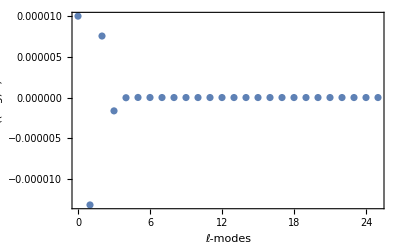

```mathematica
ListPlot[FrlReg,PlotRange->All,Frame->True,FrameStyle->Black, FrameLabel->{Style["ℓ-modes",20,FontFamily->"Latin Modern Roman"],Style["F_r^((reg) ℓ)",20,FontFamily->"Latin Modern Roman"]},ImageSize->400]
```

The total is

```mathematica
FrWithoutTail = FrlReg[[All,2]]//Total//Re
```

2.720083428748625148475×10^-6

As a comparison, from  https://arxiv.org/pdf/1003.1860 , Fr is given by 2.720083e-6  The agreement is good already, but we can get a even more accurate result by adding the high-l tail contribution!

## High-l tail contribution

The contribution from the modes with l > l_max can be written as F_r^(l>lmax) = ∑_(l=lmax+1)^∞ F_r^((reg)l). We can  estimate this contribution (sometimes known as the high-l tail) by extrapolating the last  n̄  computed l-modes using the fitting formula  F_r^((reg)l>lmax) = ∑_(n=4)^N (D_(2n)^r)/(∏_(k=1)^n (2L -2k)(2L+2k)), where L = l+1/2.

#### Building the interpolating function

DCoeff[nbar_, n_, NN_]:         function computing the D_(2n)^r coefficients
FrLTail[nbar_,lmax_,NN_]:  function computing the high-l tail contribution

nbar:   number of l-modes considered for the extrapolation
N:          number of coefficients considered for the fit 
n:          nth coefficient

```mathematica
DCoeff[nbar_, n_, NN_] := Block[{dcoeff,l,DD},
If[n<=3, Print["n must be >= 4"];dcoeff = "coefficient is known",
dcoeff = FindFit[FrlReg[[ lmax + 2 - nbar ;; lmax + 1]], Sum[DD[2 x]/Product[(2  l + 1 - 2 k)  (2  l + 1 + 2 k), {k, 1, x}], {x, 4, NN}], Table[DD[2 nn ],{nn,4, NN}], l][[n-3, 2]];];
Return[dcoeff]];
```

Example of output:

```mathematica
DCoeff[10, 4, 6] 
DCoeff[10, 5, 6] 
DCoeff[10, 6, 6]
```

1.06436044435009463

54.6238557332786435

6333.42568827518265

```mathematica
FrLTail[nbar_,lmax_,NN_] := Sum[(DCoeff[nbar,n,NN] (-4)^-n π (-1)^(lmax+1)(lmax+1))/((2n-1)Gamma[n-lmax-1/2]Gamma[n+lmax+3/2]),{n,4,NN}];
```

Example of tail computation:

```mathematica
nbar=5;
lmax=25;
NN=6;
FrLTail[nbar,lmax,NN]
```

7.74946524753125532×10^-14

Total with two examples of tail computation:

```mathematica
FrWithoutTail+FrLTail[5,lmax,NN]
FrWithoutTail+FrLTail[10,lmax,NN]
```

2.720083506243277623788×10^-6

2.720083506251928009728×10^-6

Computing the weighted average for different values of nbar:

```mathematica
nbarmin=10;
nbarmax=15;
```

```mathematica
WeightedAvarage[NN_] := {NN, Sum[(FrLTail[nbar + 1, lmax, NN] - FrLTail[nbar, lmax, NN])/(FrWithoutTail + FrLTail[nbar, lmax, NN])*(FrWithoutTail + FrLTail[nbar + 1, lmax, NN]), {nbar, nbarmin, nbarmax - 1}]/Sum[(FrLTail[nbar + 1, lmax, NN] - FrLTail[nbar, lmax, NN])/(FrWithoutTail + FrLTail[nbar, lmax, NN]), {nbar, nbarmin, nbarmax - 1}]};
```

```mathematica
FrWithoutTail
WeightedAvarage[6]
WeightedAvarage[7]
WeightedAvarage[8]
```

2.720083428748625148475×10^-6

{6,2.720083506392×10^-6}

{7,2.7200835063541×10^-6}

{8,2.720083506219×10^-6}

```mathematica
FrTotal = (WeightedAvarage[6][[2]]+WeightedAvarage[7][[2]]+WeightedAvarage[8][[2]])/3
```

2.720083506322×10^-6

```mathematica
error = Sqrt[Variance[{WeightedAvarage[6][[2]],WeightedAvarage[7][[2]],WeightedAvarage[8][[2]]}]]
```

9.09×10^-17

```mathematica
FrTotal+error
FrTotal-error
```

2.720083506413×10^-6

2.720083506231×10^-6

As a comparison, from https://arxiv.org/pdf/1003.1860:  2.720083e−6

Related Guides

Teukolsky

Related Tech Notes

## Metadata

### Categorization

Tech Note

Teukolsky

Teukolsky`

Teukolsky/tutorial/ScalarSelfForceTutorial

### Keywords